## Introduction

For analysis in Supplementary materials section “Verify generalized OA ansatz on double delta model”.

## Main

### Solve for S

#### Numerically look for root

These equations are derived in the Supplemental materials Eqs: 62

```mathematica
Clear[j1,Δ]
{j1,Δ}={8,1};
Δhat={Δ/S(-1/j-1/k),Δ/S(-1/j+1/k),Δ/S(1/j-1/k),Δ/S(1/j+1/k)};
f[S_,j_,k_]:=Evaluate[Sum[√(1-Δhat[[i]]^2),{i,1,4}]];
Manipulate[Plot[{4S-f[S,j1,k1]},{S,0,1},AxesOrigin->{0,0},AxesLabel->{Style["K",15,Italic],Style["S",15,Italic]},PlotLabel->"{J, Δ} = "<>ToString[{j1,Δ}]],{{k1,2.5},-2,10}]
```

So there is a saddle node bifurcation

#### Solve analytically

```mathematica
solsAnalytic=Solve[4S==f[S,j,k],S];
Length[solsAnalytic]
```

8

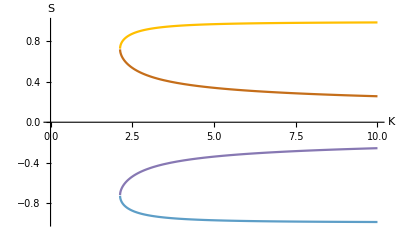

```mathematica
Plot[S/.solsAnalytic/.j->8/.k->k1//Evaluate,{k1,0,10},AxesLabel->{Style["K",15,Italic],Style["S",15,Italic]}]
```

So there are many branches. The top and stable one is given by

```mathematica
sol1=S/.solsAnalytic[[2]]
```

```mathematica
√(1/4-1/2 √(1/4-(2 (j^2+k^2))/(3 j^2 k^2)+(2^(1/3) (j^4+14 j^2 k^2+k^4))/(3 j^2 k^2 (27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))+((27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))/(3 2^(1/3) j^2 k^2))-1/2 √(1/2-(4 (j^2+k^2))/(3 j^2 k^2)-(2^(1/3) (j^4+14 j^2 k^2+k^4))/(3 j^2 k^2 (27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))-((27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))/(3 2^(1/3) j^2 k^2)-(1-(4 (j^2+k^2))/(j^2 k^2))/(4 √(1/4-(2 (j^2+k^2))/(3 j^2 k^2)+(2^(1/3) (j^4+14 j^2 k^2+k^4))/(3 j^2 k^2 (27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))+((27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3+√(-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2))^(1/3))/(3 2^(1/3) j^2 k^2)))))
```

#### Plot critical line in (J,K) space

```mathematica
Solve[-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2==0,k]/.j->8//N
```

{{k→0.},{k→0.},{k→0.-165.108 ⅈ},{k→0.+165.108 ⅈ},{k→-2.12616},{k→2.12616},{k→-1.30902+1.13978 ⅈ},{k→1.30902-1.13978 ⅈ},{k→-1.30902-1.13978 ⅈ},{k→1.30902+1.13978 ⅈ}}

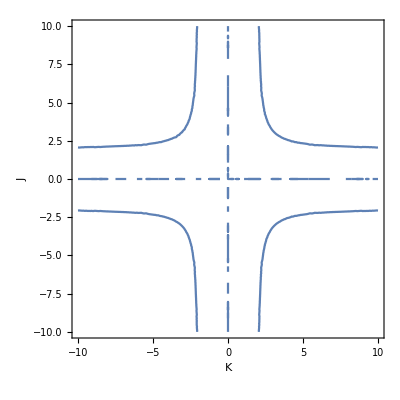

```mathematica
ContourPlot[-4 (j^4+14 j^2 k^2+k^4)^3+(27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3)^2==0,{j,-10,10},{k,-10,10},FrameLabel->{Style["K",15,Italic],Style["J",15,Italic]}]
```

Qualitatively the same as the Lorentzian. Good.

#### Simplify format for paper.

```mathematica
temp=√(1/4-1/2 √(1/4-(2 (j^2+k^2))/(3 j^2 k^2)+(2^(1/3)A)/(3 j^2 k^2 (B+√(-4 A^3+B^2))^(1/3))+((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2))-1/2 √(1/2-(4 (j^2+k^2))/(3 j^2 k^2)-A/(3 j^2 k^2 (B+√(-4 A^3+B^2))^(1/3))-((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2)-(1-(4 (j^2+k^2))/(j^2 k^2))/(4 √(1/4-(2 (j^2+k^2))/(3 j^2 k^2)+A/(3 j^2 k^2 (B+√(-4 A^3+B^2))^(1/3))+((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2)))))
```

√(1/4-1/2 √(1/4+(2^(1/3) A)/(3 (B+√(-4 A^3+B^2))^(1/3) j^2 k^2)+((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2)-(2 (j^2+k^2))/(3 j^2 k^2))-1/2 √(1/2-A/(3 (B+√(-4 A^3+B^2))^(1/3) j^2 k^2)-((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2)-(4 (j^2+k^2))/(3 j^2 k^2)-(1-(4 (j^2+k^2))/(j^2 k^2))/(4 √(1/4+A/(3 (B+√(-4 A^3+B^2))^(1/3) j^2 k^2)+((B+√(-4 A^3+B^2))^(1/3))/(3 2^(1/3) j^2 k^2)-(2 (j^2+k^2))/(3 j^2 k^2)))))

```mathematica
A=(j^4+14 j^2 k^2+k^4);
B=27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3;
B/.{j->J,k->K}//TeXForm
```

```mathematica
temp^2/.{j->J,k->K}//TeXForm
```

-\frac{1}{2} \sqrt{\frac{\sqrt[3]{2} A}{3 J^2 K^2 \sqrt[3]{\sqrt{B^2-4 A^3}+B}}+\frac{\sqrt[3]{\sqrt{B^2-4 A^3}+B}}{3 \sqrt[3]{2} J^2 K^2}-\frac{2 \left(J^2+K^2\right)}{3 J^2 K^2}+\frac{1}{4}}-\frac{1}{2}
   \sqrt{-\frac{A}{3 J^2 K^2 \sqrt[3]{\sqrt{B^2-4 A^3}+B}}-\frac{1-\frac{4 \left(J^2+K^2\right)}{J^2 K^2}}{4 \sqrt{\frac{A}{3 J^2 K^2 \sqrt[3]{\sqrt{B^2-4 A^3}+B}}+\frac{\sqrt[3]{\sqrt{B^2-4 A^3}+B}}{3
   \sqrt[3]{2} J^2 K^2}-\frac{2 \left(J^2+K^2\right)}{3 J^2 K^2}+\frac{1}{4}}}-\frac{\sqrt[3]{\sqrt{B^2-4 A^3}+B}}{3 \sqrt[3]{2} J^2 K^2}-\frac{4 \left(J^2+K^2\right)}{3 J^2 K^2}+\frac{1}{2}}+\frac{1}{4}

```mathematica
A=(j^4+14 j^2 k^2+k^4);
B=27 j^4 k^4-72 j^2 k^2 (j^2+k^2)+2 (j^2+k^2)^3;
B/.{j->J,k->K}//TeXForm
```

27 J^4 K^4-72 J^2 K^2 \left(J^2+K^2\right)+2 \left(J^2+K^2\right)^3